```mathematica
data=Import["/home/s3377910/HiggsScan/compare_eft_higgs/result_ms_ma2_only_sane"];
```

```mathematica
data=Cases[data,Except[{_,_,0}]];
```

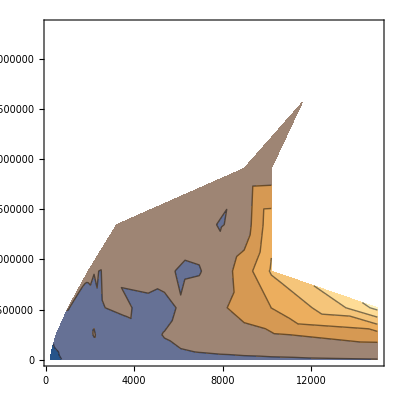

```mathematica
ListContourPlot[data]
```